## Zu Aufgabe 92

Graph der Funktion

```mathematica
f[x_,y_]:=x^2+y^2
Plot3D[f[x,y],{x,-5,5},{y,-5,5}]
```

-Graphics3D-

Höhenschichtlinien von f

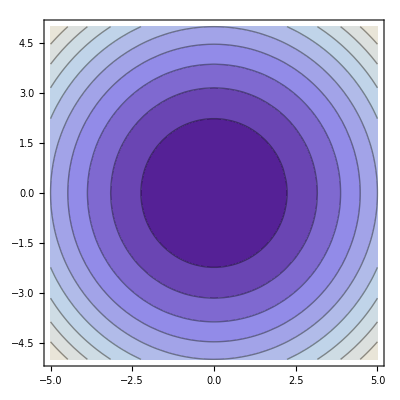

```mathematica
ContourPlot[f[x,y],{x,-5,5},{y,-5,5}]
```

## Zu Aufgabe 93

Graph der Angegeben Funktion

```mathematica
Plot3D[x^3+y^3-3*x*y,{x,-5,5},{y,-5,5}]
```

-Graphics3D-

Höhenschichtlinien

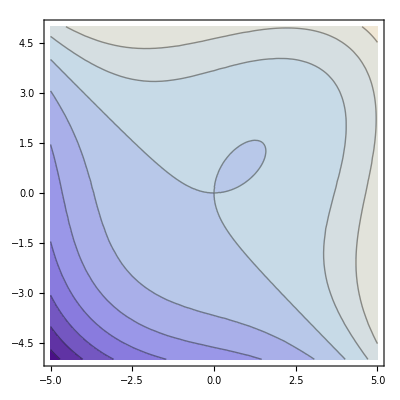

```mathematica
ContourPlot[x^3+y^3-3*x*y,{x,-5,5},{y,-5,5}]
```

Ansicht der Höhenschichtlinie für f = 0

```mathematica
PolarPlot[{3*Sin[2t]/(2*(Sin[t]^3+Cos[t]^3))},{t,-Pi/4,3*Pi/4}]
```

-Graphics-

Nullstellen des Nenners

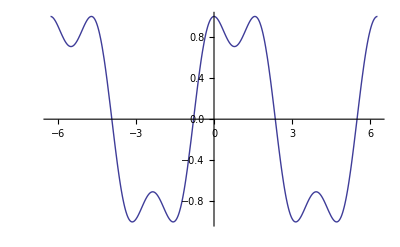

```mathematica
Plot[Sin[t]^3+Cos[t]^3,{t,-2Pi,2Pi}]
```

```mathematica
Höhenschichtlinie für f=0 und Linie, wo keine Auflösung nach y möglich ist. Im Schnitpunkt ist D[2,f]=0, alo der Gradient von f parallel zur x-Achse!
```

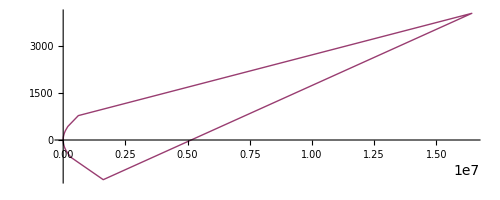

```mathematica
PolarPlot[{3*Sin[2t]/(2*(Sin[t]^3+Cos[t]^3)),Cos[t]^2/Sin[t]^2},{t,-Pi/4,3*Pi/4}]
```